6.5-20.6 x+12.5 x^2-2 x^3

1+6.5 x-10.3 x^2+4.16667 x^3-x^4/2

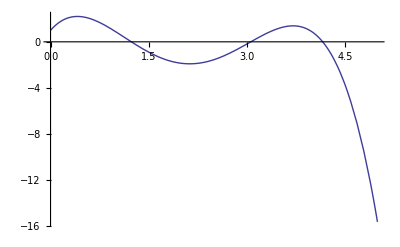

```mathematica
(*Solución exacta*)
f[x_]=-2 x^3+12.5 x^2-20.6 x+6.5
F[x_]=6.5 x-10.3 x^2+4.166666666666666 x^3-x^4/2+1
grafica1=Plot[F[x],{x,0,5},PlotRange->All]
```

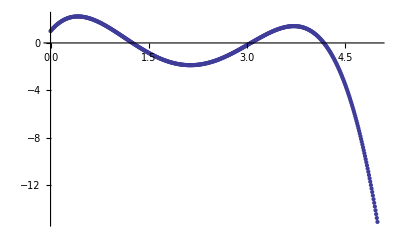

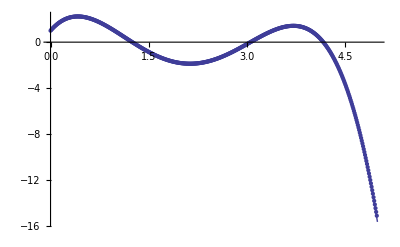

```mathematica
(*Metodo de Euler*)
x0=0;
y0=1;
h=0.01;
xf=5;
f[x_]=-2 x^3+12.5 x^2-20.6 x+6.5;
n=(xf-x0)/h;

lasx={};
AppendTo[lasx,x0];
For[i=2,i≤n,i++,
aux=x0+h (i-1);
AppendTo[lasx,aux]
]
lasx;

lasy={};
AppendTo[lasy,y0];
For[i=2,i≤n,i++,
aux=lasy[[i-1]]+f[lasx[[i-1]]]h ;
AppendTo[lasy,aux]
]

datos=Table[{lasx[[i]],lasy[[i]]},{i,1,n}];
grafica2=ListPlot[datos,PlotRange->All]
Show[grafica1,grafica2]
```